# Problem 1: Reproducing ﬁgure 7.3, (the right one only). Problem 2: Reproducing ﬁgure 7.4. Problem 3: Reproduce ﬁgure 7.11. Problem 4: simulating the time evolution of Eden cluster.

## Problem 1

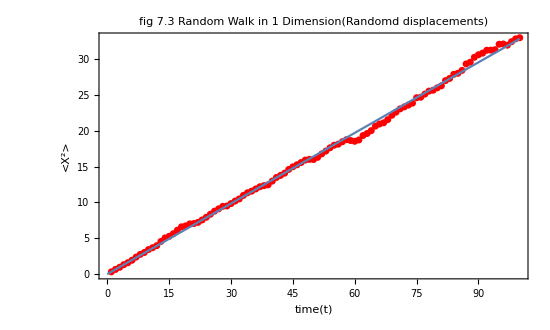

```mathematica
ClearAll["Global`*"]

(*we will identify 500 different walkers for our sample to get a good average and loop over all walkers and for each walker run a full walk using the random walking method*)
n=600; (*amount of walkers*)

(*our time interval and since there are a large number of identical particles the average collision times are roughly equally spaced and thus can e taken to be a fixed time interval adding up to 100 t intervals*)
t=100;

(*___________________________________________Initializing tables_____________________________________________________*)

xList=Table[0,{i,n}];(*a list to hold the accumulated displacements of a single walker at a given time*)
x2Ave=Table[0.0,{i,t}];
xsq=Table[0,{i,n}]; (*a list to hold the square displacements for each walker to help get te root mean square later*)

(*_____________________________________looping over timeintervals for all walkers_________________________________________*)

For[
k=1,k≤t,k++, 

(*______________________________________________looping over walkers__________________________________________________*)

For[
i=1,i≤n,i++,
If[
RandomReal[{0,1}]≥0.5,
xList[[i]]+=RandomReal[{0,1}],xList[[i]]-=RandomReal[{0,1}]]; (*fig 7.3 depicts random step lengths so we will use a random generator twice, once to randomize left or right (ie. +/- displacements) and the second time for the displacement magnitude*)

xsq[[i]]=xList[[i]]^2;
];
x2Ave[[k]]=Mean[xsq]
];

(*__________________________________________Graphing: also  remember  <x^2>=2Dt _______________________________________*)

eq1=δ*tt;
p1=Table[{i,x2Ave[[i]]},{i,t}];

(*__________________________getting the least square fir to equation 7.1: <x^2>=2Dt _______________________________________*)

twoD=δ/.FindFit[p1,eq1,δ,tt]; (*finding the slode to draw the line representing equation 7.1*)

p2=ListPlot[p1,PlotStyle->{Red}];
p3=Plot[twoD*xList,{xList,0,t}];

Show[p2,p3,PlotLabel->"fig 7.3\nRandom Walk in 1 Dimension(Randomd displacements)",AxesLabel->{"Step no ie time","<x^2>"},LabelStyle->Directive[15,Black],ImageSize->550 ,AspectRatio->0.60,PlotRange->All,Frame -> True,FrameLabel->{Style["time(t)",FontSize->15],Style["<X^2>",FontSize->15]}]
```

## Problem 2

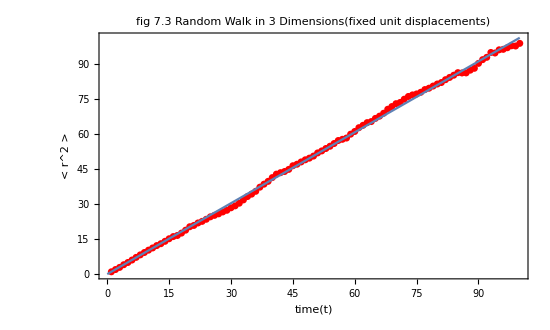

```mathematica
ClearAll["Global`*"]

(*we will repeat what we did in problem 1 but with a 3d Adaptation and unit displacements instead of 1d and random magnitudes*)
n=600; 
t=100;

(*___________________________________________Initializing tables_____________________________________________________*)

rList=Table[{0,0,0},{i,n}];
(*a list to hold the accumulated displacements of a single walker at a given time, so r is a 2d array, each rList[[i,j]], where i represents the ith walker, and we have n many, and j the x, y or z direction so we have 3 directions, so rList[[1,2]] would specify the first walker and its accumulated displacement along the y axis *)

rsq=Table[0,{i,n}]; (*a list to hold the square displacements for each walker to help get te root mean square later*)
r2Ave=Table[0.0,{i,t}];

(*_____________________________________looping over timeintervals for all walkers_________________________________________*)
For[
k=1,k≤t,k++, 

(*____________________________________________looping over walkers__________________________________________________*)

For[
i=1,i≤n,i++,
(*we have 6 possible directions in 3d - 2 for each single dimension, similar to our previous left/right for 1D so we divide our probabilities into 6 sections and distribute the possibilities between the 6 random intervals and accumulate displacement along the specified direction by a simgle unit 1*)
rando=RandomReal[{0,1}];

If[rando≤1/6,rList[[i,1]]++,
If[rando≤2/6,rList[[i,1]]--,
If[rando≤3/6,rList[[i,2]]++,
If[rando≤4/6,rList[[i,2]]--,
If[rando≤5/6,rList[[i,3]]++,
rList[[i,3]]--]]]]]; 

rsq[[i]]=rList[[i,3]]^2+rList[[i,2]]^2+rList[[i,1]]^2;(*Magnitude of the 3D accumulated displacement*)
];
r2Ave[[k]]=Mean[rsq]
];

(*__________________________________________Graphing: also  remember  <r^2>=2Dt _______________________________________*)

eq1=δ*tt;
p1=Table[{i,r2Ave[[i]]},{i,t}];

(*__________________________getting the least square fir to equation 7.1: <r^2>=2Dt _______________________________________*)

twoD=δ/.FindFit[p1,eq1,δ,tt]; (*finding the slode to draw the line representing equation 7.1*)

p2=ListPlot[p1,PlotStyle->{Red}];
p3=Plot[twoD*rList,{rList,0,t}];

Show[p2,p3,PlotLabel->"fig 7.3\nRandom Walk in 3 Dimensions(fixed unit displacements)",AxesLabel->{"Step no ie time","<x^2>"},LabelStyle->Directive[15,Black],ImageSize->550 ,AspectRatio->0.60,PlotRange->All,Frame -> True,FrameLabel->{Style["time(t)",FontSize->15],Style["< r^2 >",FontSize->15]}]
```

## Problem 3

```mathematica
ClearAll["Global`*"]
(*__________________________Initializing parameters and setting up tables based on figure 7.11 _____________________________*)

dx=dy=1; d=1; dt=0.25;xList=yList=Range[-10,10,dx]; tMax=20 dt; tList=Range[0,tMax,dt];
lt=Length[tList];lx=Length[xList];ly=Length[yList];
ρ=Table[.0,{i,lt},{k,lx},{k,ly}]; (*table for the 2-D time dependent density values*)

tmp=0*tList; h=0*tList;(*intermediate/provisional storage lists for sequantial plotting*)

(*___________________Positioning our density as a gaussian like occurence in the middle of the plot at t=1____________________*)

ymid=Position[yList,0] //.{x_}:>x; xmid=Position[xList,0] //.{x_}:>x; (*a rule to extract/ replace all bracketed terms with bracket free terms and since we have the output as a single bracket this rule removes all 1st order lists *)

For[
i=xmid-2,i≤xmid+2,i++, 
For[
k=ymid-2,k≤ymid+2,k++,
ρ[[1,i,k]]=1; 
]
]
(* ρ=1 since we want a 4 unit wide starting distribution around the middle, +/- 2 left and right *)


tmp[[1]]=Table[{xList[[i]],yList[[k]],ρ[[1,i,k]]},{i,lx},{k,ly}]//Flatten; (*for t=1*)
h[[1]]=Table[{tmp[[1,i]],tmp[[1,i+1]],tmp[[1,i+2]]},{i,1,Length[tmp[[1]]]-2,3}];


(*__________________________________________Running the diffusion steps _______________________________________*)

Monitor[
For[
n=2,n≤lt,n++, (*loop over collision intervals i.e time*)
For[
k=2,k<ly,k++,(*loop over x intervals*)
For[
i=2,i<lx,i++, (*loop over y intervals*)
ρ[[n,i,k]]=ρ[[n-1,i,k]]+d (dt/4 dx^2)(ρ[[n-1,i+1,k]]+ρ[[n-1,i-1,k]]+ρ[[n-1,i,k+1]]+ρ[[n-1,i,k-1]]-4ρ[[n-1,i,k]]);

tmp[[n]]=Table[{xList[[i]],yList[[k]],ρ[[n,i,k]]},{i,lx},{k,ly}]; 
tmp[[n]]=Flatten[tmp[[n]]];

h[[n]]=Table[{tmp[[n,i]],tmp[[n,i+1]],tmp[[n,i+2]]},{i,1,Length[tmp[[n]]]-2,3}];
]
]
]
,ProgressIndicator[n,{2,lt+1}]]
```

```mathematica
(*__________________________________________Graphing the initial distribution _______________________________________*)

{ListPlot3D[h[[1]],AxesLabel->{"x","y","ρ"},PlotLabel->"fig 7.11 at t=1 ",PlotRange->{All,All,{0,1}},ColorFunction->"BlueGreenYellow",Mesh->20,PlotLegends->Automatic,ImageSize->240],



(*________________________________________Graphing the subsequent distribution _______________________________________*)

ListPlot3D[h[[8]],AxesLabel->{"x","y","ρ"},PlotLabel->"fig 7.11 at t=7dt ",PlotRange->{All,All,{0,1}},ColorFunction->"BlueGreenYellow",Mesh->20,PlotLegends->Automatic,ImageSize->240],
ListPlot3D[h[[21]],AxesLabel->{"x","y","ρ"},PlotLabel->"fig 7.11 at t=20dt ",PlotRange->{All,All,{0,1}},ColorFunction->"BlueGreenYellow",Mesh->20,PlotLegends->Automatic,ImageSize->240]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Problem 4

```mathematica
ClearAll["Global`*"] 


p=1000; (*number of particles*)
xList=yList=Range[-40,40]; lx=Length[xList]; ly=Length[yList];
midx=Position[xList,0]//.{x_}:>x;  midy=Position[yList,0]//.{x_}:>x; ; 

pos=Table[0,{i,lx},{j,ly}];
pos[[midx,midy]]=1; (*initial condition*)
occup={{midx,midy}}; (*array for occupied points*)

(*________________________________________arranging the cluster Grid_______________________________________*)

sites=Table[i+(j-1)ly,{j,1,ly},{i,1,lx}]; 

(*numbering the grid:*)
cluster = Array[0 &,{lx + 2, ly + 2}] ;
cluster[[2;;lx+1,2;;ly+1]] = sites;cluster[[1]] = cluster[[lx+1]];cluster[[All,1]] = cluster[[All,ly+1]];
cluster[[lx+2]] = cluster[[2]];
cluster[[All,ly+2]] = cluster[[All,2]];

nT=Table[0,{i,lx*ly},{j,4}]; (*neighbours table*)

k = 1; (*from assignment 11, similar to Dr's code*)
Do[
nT[[k,1]] = cluster[[i,j+1]];
nT[[k,2]] = cluster[[i+1,j]];
nT[[k,3]] = cluster[[i,j-1]];
nT[[k,4]] = cluster[[i-1,j]]; k++,
{i,2,lx+1},{j,2,ly+1}];

pp=Table[0,{i,p}];
pp[[1]]=ArrayPlot[pos];


Monitor[
For[n=2,n≤p,n++,

(*_________Setting up filled and non filled coordinates and the locations of their adjacents on the grid____________________*)

emptyList={}; temp={}; 

For[
k=1,k≤Length[occup],k++,
ny=occup[[k,2]];
nx=occup[[k,1]];
AppendTo[temp,nT[[sites[[nx,ny]]]]] 
];

temp=Flatten[temp];
temp=DeleteDuplicates[temp];

For[
l=1,l<=Length[temp],l++,
If[
pos[[Position[sites,temp[[l]]][[1,1]],Position[sites,temp[[l]]][[1,2]]]]==0,AppendTo[emptyList,temp[[l]]]] 
];

pRand=RandomReal[];
xRand=Position[sites,emptyList[[Floor[pRand*Length[emptyList]]+1]]][[1,1]]; yRand=Position[sites,emptyList[[Floor[pRand*Length[emptyList]]+1]]][[1,2]]; 

AppendTo[occup,{xRand,yRand}];
pos[[xRand,yRand]]=1;
pp[[n]]=ArrayPlot[pos,ColorRules->{1->Black,0->Orange}]
],ProgressIndicator[n,{2,p+1}]];

st={FontColor->GrayLevel[.7]};

Framed[Manipulate[pp[[t]],{t,1,p,1,AnimationRate->10,Appearance->"Open"},Paneled->False,FrameLabel->{Style["Eden Cluster Time Evolution",FontSize->12]}],RoundingRadius->20,Background->Black,BaseStyle->st]
```

Part::partd: Part specification pp⟦116⟧ is longer than depth of object.